9.79821

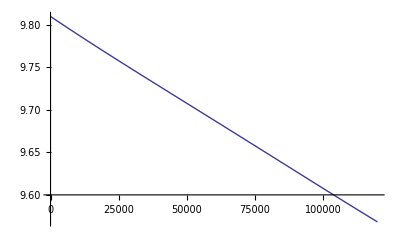

```mathematica
LBase[nodes_, k_]:=(
l=1;
For[i=1,i≤Length[nodes],i++,
If[i≠k,
l*=(x-nodes[[i]])/(nodes[[k]]-nodes[[i]])
]
];
l
)
LPoly[nodes_,values_]:=(
poly=0;
For[k=1,k≤Length[nodes],k++,
poly+=values[[k]]*LBase[nodes,k]
];
poly//Expand
)
nodes=Range[0,120000,30000];
values={9.81, 9.7478, 9.6879, 9.6278, 9.5682};
g[x_]=LPoly[nodes,values];
g[5500]
Plot[g[x],{x,0,120000}]
```